```mathematica
delta:=0.01;
```

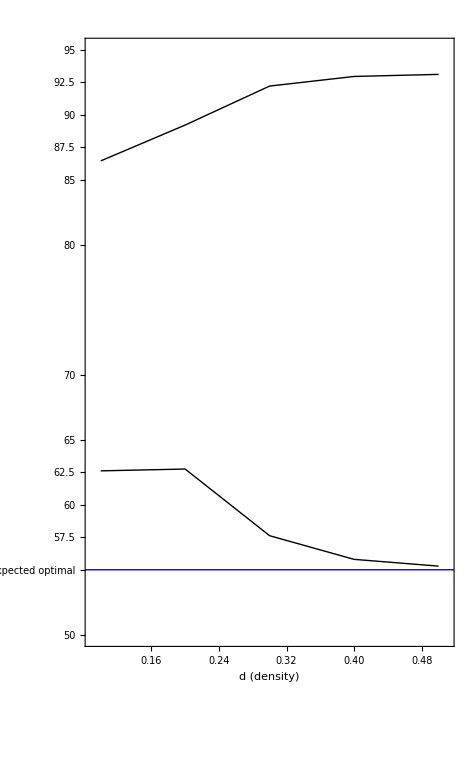

```mathematica
t1:={   {0.1,62.61},{0.2,62.75},{0.3,57.62},{0.4,55.80},{0.5,55.28}     };
t2:={   {0.1,86.46},{0.2,89.22},{0.3,92.22},{0.4,92.96},{0.5,93.12}     };
opt12:={ {0,55} ,{1,55}};
ListLinePlot[
{t1,t2,opt12},
AspectRatio->GoldenRatio,
PlotRange->{{0.1-delta,0.5+delta},{50,95}},AxesOrigin->{0.1-delta,50},
Ticks->{Automatic,{50,60,57.5,65,70,80,90,{55, "expected\noptimal"},62.5,85,87.5,95 ,92.5   }},
PlotStyle->{   {Thickness[Large],Black},{Thickness[Large],Black},{Thickness[Large],Blue}  },
Frame->True,FrameLabel->{Style["d (density)",FontSize->20],Style["f̄ (average)",FontSize->20]}
]
```

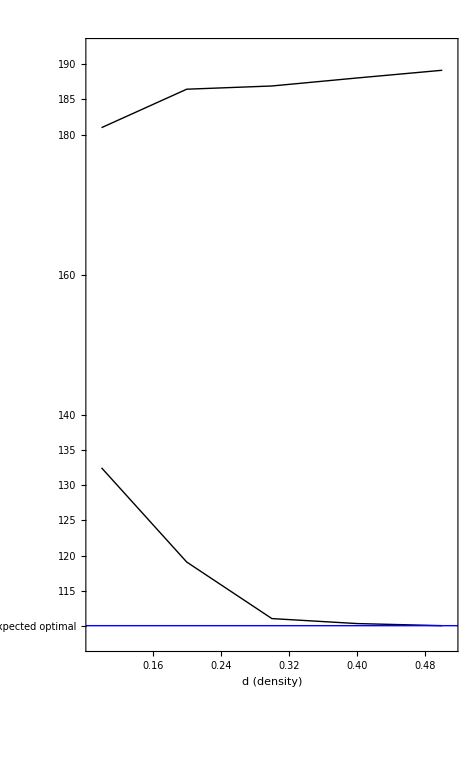

```mathematica
t3:={   {0.1,132.50},{0.2,119.07},{0.3,111.01},{0.4,110.30},{0.5,110.00}     };
t4:={   {0.1,180.98},{0.2,186.46},{0.3,186.92},{0.4,188.06},{0.5,189.16}     };
opt34:={ {0,110} ,{1,110}};
ListLinePlot[
{t3,t4,opt34},
AspectRatio->GoldenRatio,
PlotRange->{{0.1-delta,0.5+delta},{108,192}},AxesOrigin->{0.1-delta,108},
Ticks->{Automatic,{120,130,140,160,180,190,{110, "expected\noptimal"} ,115,125,135,185  }},
PlotStyle->{   {Thickness[Large],Black},{Thickness[Large],Black},{Thickness[Large],Blue}  },
Frame->True,FrameLabel->{Style["d (density)",FontSize->20],Style["f̄ (average)",FontSize->20]}
]
```